# Lab 13: Harmonic Motion

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Click here to see a famous harmonic oscillator
```

### Simple Harmonic Motion

Simple harmonic motion plays a central role in much of physics and engineering.  The description is used widely for disparate phenomena such as oscillations in an AC circuit, the bending of a bridge, and the quantum mechanics of light. The prototypical simple harmonic oscillator is a mass on an ideal spring (i.e. one which obeys Hooke’s Law). The restoring force provided by the spring is F=-k x where x is the displacement from equilibrium and k is the spring constant. 

The equation of motion for the mass is

m (d^2 x)/(d t^2)  = -k x

which we can rewrite as

(d^2 x)/(d t^2) + ω^2 x= 0           (1)

where

ω = √(k/m)

is called the “angular frequency” of the system (not to be confused with the “frequency” f = ω/(2π))

Equation (1) is a second order differential equation to solve for x(t). There are two very common forms for the general solution of this equation:

#### Solution 1: Sines and Cosines

The solution of (1) will be a function which, when differentiated twice, will give us the original function times a constant.  The obvious choice is either sine or cosine.  However, this is a second-order differential equation, so there need to be two arbitrary constants in the full general solution.  Let’s use a linear combination of both sine and cosine:

```mathematica
x1[t_]=A Cos[w t]+B Sin[w t]
```

A Cos[t w]+B Sin[t w]

Right now, there appear to be three undetermined constants (A, B, and w), but we will see that one of them is fixed by the equation of motion (1)

```mathematica
eqn1=D[x1[t], {t, 2}]+ω^2 x1[t]
```

-A w^2 Cos[t w]-B w^2 Sin[t w]+ω^2 (A Cos[t w]+B Sin[t w])

We can collect the terms in the sine and the cosine together using the Mathematica command Collect. The syntax for Collect is

```mathematica
?Collect
```

RowBox[{"Collect", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["x", "TI"]}], "]"}] collects together terms involving the same powers of objects matching StyleBox["x", "TI"]. 
RowBox[{"Collect", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] collects together terms that involve the same powers of objects matching SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], …. 
RowBox[{"Collect", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["var", "TI"], ",", StyleBox["h", "TI"]}], "]"}] applies StyleBox["h", "TI"] to the expression that forms the coefficient of each term obtained.

Collecting the sine and cosine terms

```mathematica
Collect[eqn1,{A,B}]
```

A (-w^2 Cos[t w]+ω^2 Cos[t w])+B (-w^2 Sin[t w]+ω^2 Sin[t w])

shows that the differential equation will be satisfied for all A and B if w=ω. The constants A and B are (at this point) arbitrary constants and will be determined by the initial conditions. In fact, A is the initial displacement of the oscillator

```mathematica
x1[0]
```

A

and B is v(0)/w as can be seen by differentiating x[t] to get the velocity and then checking the velocity at t=0.

```mathematica
v1[t_]=D[x1[t],t]
v1[0]
```

B w Cos[t w]-A w Sin[t w]

B w

#### Solution 2: Just Cosine

We chose a linear combination of sines and cosines above which solved equation (1), but this parameterization is not unique.  Since sin(x+ϕ)=sin(x) cos(ϕ)+cos(x) sin(ϕ), we can rewrite our solution so that it contains only cosines!  However, since we still need two arbitrary constants, we pick up an extra piece in the argument of the cosine:

```mathematica
x2[t_]=A2 Cos[w t+ϕ]
```

A2 Cos[t w+ϕ]

Here ϕ is a constant called the phase angle. This solution is equivalent to Solution 1!  The only difference is how we parameterize it; sometimes the first solution is more convenient, sometimes not.  A2 is not, in general, the same constant as A for a given set of initial conditions.

Putting this back into our equation for simple harmonic motion gives

```mathematica
eqn2=D[x2[t], {t, 2}]+ω^2 x2[t]
Simplify[eqn2]
```

-A2 w^2 Cos[t w+ϕ]+A2 ω^2 Cos[t w+ϕ]

A2 (-w^2+ω^2) Cos[t w+ϕ]

which shows that, as before, this is a solution for all times t if ω=w.  

We can discover the physical significance of ϕ by looking at x[0] and v[0].

```mathematica
x2[0]
```

A2 Cos[ϕ]

```mathematica
v2[t_]=D[x2[t],t]
v2[0]
```

-A2 w Sin[t w+ϕ]

-A2 w Sin[ϕ]

We can see that the constant A2 fixes the amplitude of the oscillations, while the phase angle ϕ allows us to set the initial values x(t) and v(t).  Note that, for a given amplitude, there is always a choice of B and ϕ such that our two solutions coincide!

```mathematica
Manipulate[Plot[{x1[t]/.{A->1,B->0,w->1},x2[t]/.{A2->1,w->1,ϕ->p}},{t,0,2π},AxesLabel->{"t","x(t)"}],{p,0,2π}]
```

Note also that

```mathematica
v[0]/x[0]
```

-w Tan[ϕ]

so that the phase angle ϕ is given by ϕ=ArcTan[v[0]/(w x[0])]. Thus, if v(0)=0, ϕ=0 or π. If x(0)=0, then ϕ=π/2 or 3π/2.  We can see this by looking at a plot of the tangent.

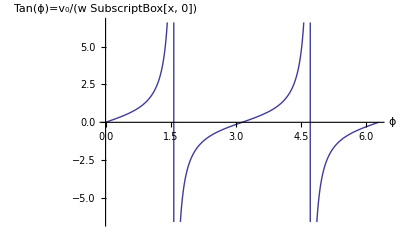

```mathematica
Plot[Tan[ϕ],{ϕ,0,2 π},AxesLabel->{"ϕ","Tan(ϕ)=v_0/(w SubscriptBox[x, 0])"}]
```

#### Energy Conservation in Simple Harmonic Motion

(Below, we are using Solution 2, x(t)=A2 Cos[w t + ϕ]; it is more useful for now!)

Energy is conserved in simple harmonic motion since there are no dissipative forces. During the motion the energy sloshes back and forth between kinetic and potential energy. The kinetic energy is

```mathematica
KE[t_]=1/2 m v2[t]^2
```

1/2 A2^2 m w^2 Sin[t w+ϕ]^2

and the potential energy is

```mathematica
U[t_]=1/2 k x2[t]^2
```

1/2 A2^2 k Cos[t w+ϕ]^2

The total energy is

```mathematica
Energy[t_]=KE[t]+U[t]
```

1/2 A2^2 k Cos[t w+ϕ]^2+1/2 A2^2 m w^2 Sin[t w+ϕ]^2

Since ω=√(k/m) we have

```mathematica
Simplify[Energy[t]/.w->√(k/m)]
```

(A2^2 k)/2

which does not depend on time!  This shows that the energy is constant throughout the motion. 

Suppose we start our oscillator with v[0]=0 and x[0] =10cm. Then ϕ=0 and A2=10cm. Suppose further that m=0.1kg and k=1 N/m so that ω=√10 sec^-1 and the total energy of the oscillator is E=1/2(.1)^2 J=.05 J . We can plot the kinetic and potential energies as a function of time. With these values we have an oscillator with a period of just under two seconds. Recall that the period T is given by T=2 π/ω.

```mathematica
oscillatorConditions={A2->.1,m->.1,w->√(k/m),ϕ->0,k->1}
```

{A2→0.1,m→0.1,w→√(k/m),ϕ→0,k→1}

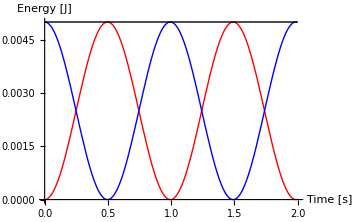

```mathematica
Plot[{Tooltip[KE[t]//.oscillatorConditions,"Kinetic Energy"],Tooltip[U[t]//.oscillatorConditions,"Potential Energy"],Tooltip[Energy[t]//.oscillatorConditions,"Total Energy"]},{t,0,2},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1],RGBColor[0,0,0]},AxesLabel->{"Time [s]","Energy [J]"}]
```

Recall that the short hand //. stands for ReplaceAllRepeated which applies the replacement rules until the expression stops changing.  We also use for the first time Tooltip; hover your cursor over the functions in the plot to see the effect!

#### Animations!

We will animate the mass and spring system undergoing simple harmonic motion. We will need to make four objects: a mass, a spring, a surface for the mass to slide on, and a wall to anchor the spring to. We will start with the mass which must oscillate with time. We will use the graphics primitive Rectangle to draw the mass. The syntax for Rectangle is

```mathematica
?Rectangle
```

RowBox[{"Rectangle", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] is a two-dimensional graphics primitive that represents a filled rectangle, oriented parallel to the axes. 
RowBox[{"Rectangle", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], "]"}] corresponds to a unit square with its bottom-left corner at RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}].

The masses left edge is at x=1 and t=0 while its right edge is at x=2 and t=0. It has a height of 1/2 and I have colored it red using RGBColor. Style directives such as RGBColor must come before the graphics primitive. The style directives and the graphics primitives are enclosed in a list and then passed to Graphics or Graphics3D.

```mathematica
mass[t_]:=Graphics[{RGBColor[1,0,0],Rectangle[{1+x2[t]//.oscillatorConditions,0},{2+x2[t]//.oscillatorConditions,1/2}]}]
```

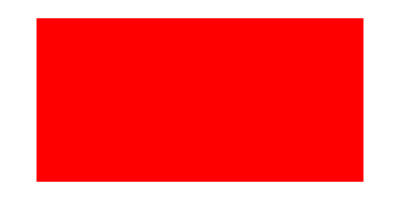

```mathematica
Show[mass[0]]
```

Next, we make our surface. I have put the surface a little bit below zero so that when we are all finished our mass rides on it. I determined how far below zero I needed the surface by trial and error.

```mathematica
?Line
```

RowBox[{"Line", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] is a graphics primitive that represents a line joining a sequence of points. 
RowBox[{"Line", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["21", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of lines.

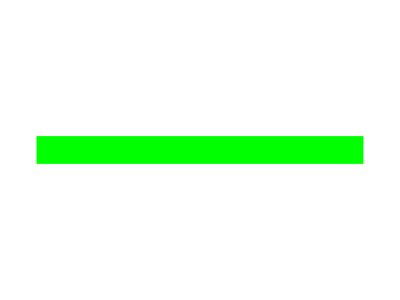

```mathematica
surface=Graphics[{Thickness[0.05],RGBColor[0,1,0],Line[{{0,-1/20},{3,-1/20}}]}]
```

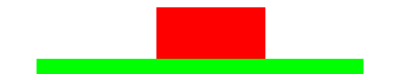

```mathematica
Show[surface,mass[0],AspectRatio->Automatic]
```

The next step is the attach our spring to the mass.

```mathematica
spring[t_]:=Graphics[{Thickness[0.015],Line[{{0,1/4},{1+x2[t]//.oscillatorConditions,1/4}}]}]
```

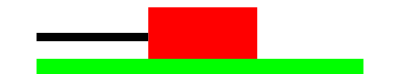

```mathematica
Show[surface,mass[π/2],spring[π/2],AspectRatio->Automatic]
```

Lastly, we make the wall and put everything together.

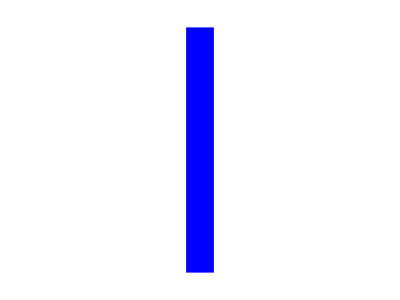

```mathematica
wall=Graphics[{Thickness[0.05],RGBColor[0,0,1],Line[{{0,-1/20},{0,1}}]}]
```

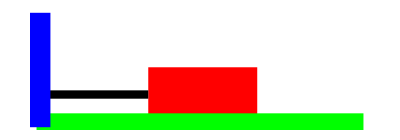

```mathematica
Show[surface,mass[π/2],spring[π/2],wall,AspectRatio->Automatic]
```

Now for the animation!

```mathematica
ListAnimate[Table[Show[surface,mass[t],spring[t],wall,AspectRatio->Automatic],{t,0,2,1/16}]]
```

We can keep track of how much of the total energy is kinetic energy and how much is potential energy by drawing two rectangles whose heights are proportional to the kinetic and potential energies respectively. The rectangles are called "KEbar" and "Ubar" and are functions of time.

```mathematica
KEbar[t_]:=Graphics[{RGBColor[1,0,0],Rectangle[{3.5,0},{3.75,40 KE[t]}]}]//.oscillatorConditions;
Ubar[t_]:=Graphics[{RGBColor[0,0,1],Rectangle[{3.25,0},{3.5,40 U[t]}]}]//.oscillatorConditions;
```

The two rectangles can be labeled by using the graphics primitive Text. Text[expression,{x,y}] is a graphics primitive that gives the printed form of the expression centered at {x,y}. As with all graphics primitives you must make them graphics objects before using them in Show. The labels are called "labelOne" and "labelTwo".

```mathematica
labelOne=Graphics[Text["KE",{3.625,0.5}]];
labelTwo=Graphics[Text["PE",{3.3725,0.5}]];
```

Our final animation is shown below.

```mathematica
ListAnimate[Table[Show[surface,mass[t],spring[t],wall,KEbar[t],Ubar[t],labelOne,labelTwo,AspectRatio->Automatic],{t,0,2,1/16}]]
```

Fun, no?

#### Phase Space plots

Another way of looking at the motion is to plot the particle's velocity versus the particle's position. This is called a phase space plot. This is useful because a particle undergoing simple harmonic motion will be at any given position twice in a single period but will have different velocities depending on whether it is moving to the right or to left (spring is expanding or contracting). You can see this from the plot below. Notice that the particle is at x=0 twice. Once at roughly t=0.5 seconds and once at roughly t=1.5 seconds. When t=0.5 the particle has a velocity of 1.265 to the left. At t=1.5 the particle has a velocity of 1.265 to the right.

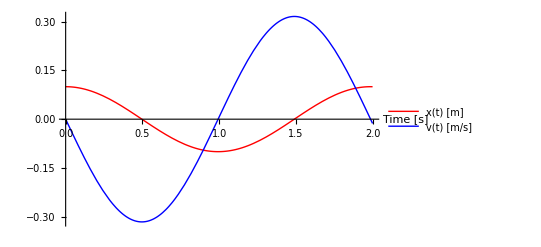

```mathematica
Plot[{Tooltip[x2[t]//.oscillatorConditions,"x(t)"],Tooltip[v2[t]//.oscillatorConditions,"v(t)"]},{t,0,2},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},AxesLabel->{"Time [s]",""},PlotLegends->{"x(t) [m]","v(t) [m/s]"}]
```

We can make a phase space plot by using the function ParametricPlot. The syntax is

```mathematica
?ParametricPlot
```

RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a parametric plot of a curve with StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]] as a function of StyleBox["u", "TI"]. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several parametric curves. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots a parametric region. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several parametric regions.

Our phase space plot is shown below.

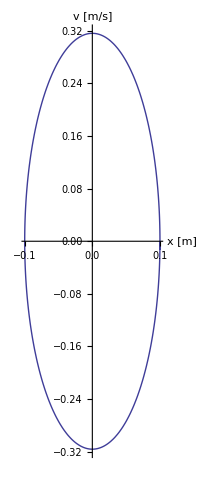

```mathematica
ParametricPlot[{x2[t]//.oscillatorConditions,v2[t]//.oscillatorConditions},{t,0,2},AspectRatio->Full,AxesLabel->{"x [m]","v [m/s]"}]
```

### Damped Harmonic Motion

Up until now we have assumed that our oscillator does not lose any energy. Thus, if our oscillator is a mass and spring system, it is one without friction. If our oscillator is a circuit, it is a circuit without resistance. However, most real systems have some dissipative forces and undergo damped harmonic motion. 

The equation of motion for an object undergoing damped harmonic motion is

(d^2 x)/(d t^2) + γ (d x)/(d t)  + ω^2 x= 0        (2)

where γ is the damping parameter. Notice that the dissipative force is velocity-dependent, just as it is for air resistance. Translated into Mathematica our equation is

```mathematica
Clear[x,v,KE,U,ϕ,A,B, c]
dampedEquation=D[x[t], {t, 2}]+γ D[x[t], t]+ω^2 x[t]
```

ω^2 x[t]+γ x'[t]+x''[t]

To solve this equation we will guess that the solution is of the form

x(t)= A ⅇ^(B t) cos( c t + ϕ)

There is no guarantee that this will work, but it is not a completely arbitrary guess; we have some reasonable idea of what the function should do, even if we don’t know exactly what it should look like.  We call this kind of educated guess an “ansatz”, and we do it all the time in physics. 

It looks again like we have more constants (A, B, c, and ϕ) than we need (only 2), but we will see that satisfying the equation of motion (2) will fix two of them for us.

We must substitute our ansatz for x[t] into the equation and see if it works. This is tedious to do by hand, but it is quite easy to do with Mathematica. Our guess is

```mathematica
x[t_]=A ⅇ^(B t) Cos[c t+ϕ]
```

A ⅇ^(B t) Cos[c t+ϕ]

and putting this into the equation for the damped oscillator gives

```mathematica
dampedEquation
```

A B^2 ⅇ^(B t) Cos[c t+ϕ]-A c^2 ⅇ^(B t) Cos[c t+ϕ]+A ⅇ^(B t) ω^2 Cos[c t+ϕ]-2 A B c ⅇ^(B t) Sin[c t+ϕ]+γ (A B ⅇ^(B t) Cos[c t+ϕ]-A c ⅇ^(B t) Sin[c t+ϕ])

Notice that each term has a factor of A and a factor of Exp[B t] in front of it. We can pull these factors out of the equation by using Collect.

```mathematica
dampedEquation=Collect[dampedEquation,{A,ⅇ^(B t)}]
```

A ⅇ^(B t) (B^2 Cos[c t+ϕ]-c^2 Cos[c t+ϕ]+B γ Cos[c t+ϕ]+ω^2 Cos[c t+ϕ]-2 B c Sin[c t+ϕ]-c γ Sin[c t+ϕ])

We want our damped equation to be equal to zero at all times t, so we can discard the overall factor of A Exp[B t]. What we are left with is the third part (that is, the third factor) of the damped equation.

```mathematica
dampedEquation⟦3⟧
```

B^2 Cos[c t+ϕ]-c^2 Cos[c t+ϕ]+B γ Cos[c t+ϕ]+ω^2 Cos[c t+ϕ]-2 B c Sin[c t+ϕ]-c γ Sin[c t+ϕ]

We can collect the sine and the cosine terms together, which gives

```mathematica
NewEquation=Collect[dampedEquation⟦3⟧,{Sin[c t+ϕ],Cos[c t+ϕ]}]
```

(B^2-c^2+B γ+ω^2) Cos[c t+ϕ]+(-2 B c-c γ) Sin[c t+ϕ]

The sine and the cosine are 90 degrees out of phase with each other. In other words when the sine is zero, the cosine is one. Thus, the only way the equation can equal zero at all times is for the sine and cosine terms to vanish separately. The coefficient of the sine term is

```mathematica
NewEquation⟦2,1⟧//Simplify
```

-c (2 B+γ)

and requiring that this vanishes gives

```mathematica
solution1=First[Solve[NewEquation⟦2,1⟧==0,B]]
```

{B→-γ/2}

Thus B=-γ/2. Putting this back into the coefficient of the cosine term and requiring that this coefficient also vanishes giving two solutions for c.

```mathematica
solution2=Solve[(NewEquation⟦1,1⟧/.solution1)==0,c]
```

{{c→-1/2 √(-γ^2+4 ω^2)},{c→1/2 √(-γ^2+4 ω^2)}}

We want c to correspond to a frequency, so we throw away the negative solution as unphysical.  As a result, our guess solves the equation if

```mathematica
B=B/.solution1
c=c/.solution2⟦2⟧
```

-γ/2

1/2 √(-γ^2+4 ω^2)

Notice that if the damping is small, c (which is often called ω') is almost the same as ω. With these values for B and c our solution is

```mathematica
x[t]
```

A ⅇ^(-(t γ)/2) Cos[ϕ+1/2 t √(-γ^2+4 ω^2)]

Thus, there are only two arbitrary constants A and ϕ in our general solution, as expected.  These constants are determined by the initial conditions. 

In fact, x[0]=ACos[ϕ] just as in the undamped case.

```mathematica
x[0]
```

A Cos[ϕ]

The phase angle ϕ is a little more complicated. The velocity is

```mathematica
Clear[v]
v[t_]=Simplify[D[x[t], t]]
```

-1/2 A ⅇ^(-(t γ)/2) (γ Cos[ϕ+1/2 t √(-γ^2+4 ω^2)]+√(-γ^2+4 ω^2) Sin[ϕ+1/2 t √(-γ^2+4 ω^2)])

so the initial velocity is

```mathematica
v[0]
```

-1/2 A (γ Cos[ϕ]+√(-γ^2+4 ω^2) Sin[ϕ])

If we substitute A=x0/Cos[ϕ] into v[0] and simplify we get

```mathematica
A=x0/Cos[ϕ];
v[0]=Simplify[v[0]]
```

-1/2 x0 (γ+√(-γ^2+4 ω^2) Tan[ϕ])

Solving this for the initial velocity in terms of ϕ gives

```mathematica
ϕSolution=Solve[v0==v[0],ϕ]
```

{{ϕ→ConditionalExpression[ArcTan[(-2 v0-x0 γ)/(x0 √(-γ^2+4 ω^2))]+π C[1],C[1]∈Integers]}}

The warning message is a reminder that we must be careful to get the correct branch of the inverse trig function. If the damping factor gamma is zero, we recover our previous result.

```mathematica
PowerExpand[ϕSolution/.γ->0]
```

{{ϕ→ConditionalExpression[-ArcTan[v0/(x0 ω)]+π C[1],C[1]∈Integers]}}

In general ϕ is given by

```mathematica
ϕ=-ArcTan[v0/(x0 ω)]
```

-ArcTan[v0/(x0 ω)]

All damped oscillators fall into one of three special cases:

a) If 4 ω^2-γ^2>0, the oscillator is underdamped 

b) If 4 ω^2-γ^2=0, the oscillator is critically damped 

c) If 4 ω^2-γ^2<0, the oscillator overdamped. 

We will look at each of these cases in turn.

#### UnderDamping

If γ<2ω  the oscillator is underdamped.

```mathematica
UnderDampedConditions={x0->.1,m->.1,ω->√(k/m),v0->0,k->1,γ->.1}
```

{x0→0.1,m→0.1,ω→√(k/m),v0→0,k→1,γ→0.1}

Notice that the motion is given by an oscillatory piece (the cosine) damped by an exponential

0.1 ⅇ^(-0.05 t) Cos[0.+3.16188 t]

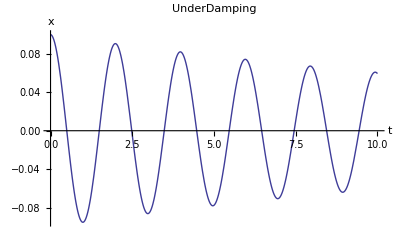

```mathematica
x[t]//.UnderDampedConditions
Plot[x[t]//.UnderDampedConditions,{t,0,10},PlotLabel->"UnderDamping",AxesLabel->{"t","x"}]
```

We can plot the damping envelope, which is Exp[(-γ/2)t], along with the position of the oscillator:

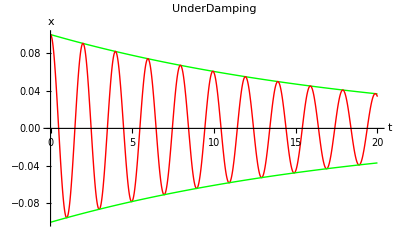

```mathematica
Plot[{x0 ⅇ^(B t)//.UnderDampedConditions,x[t]//.UnderDampedConditions,-x0 ⅇ^(B t)//.UnderDampedConditions},{t,0,20},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0]},PlotLabel->"UnderDamping",AxesLabel->{"t","x"}]
```

The phase space plot for the damped oscillator is very different from the phase space plot for the undamped oscillator. The motion of the undamped oscillator is periodic, and as a result the phase space plot is closed.  The damped oscillator's motion is not periodic, therefore its phase plot is not closed. The phase space plot spirals in as the particle loses energy.

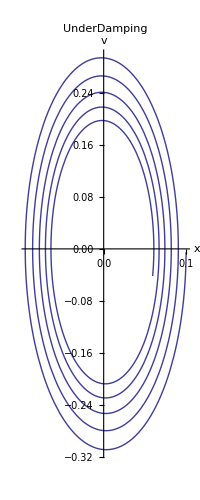

```mathematica
ParametricPlot[{x[t]//.UnderDampedConditions,v[t]//.UnderDampedConditions},{t,0,10},AxesLabel->{"x","v"},PlotLabel->"UnderDamping\n\n",AspectRatio->Full]
```

Try a few different values of γ to see what happens to the plots.  Check to see that your result reduces to the previous (UNDAMPED) result for γ=0.

#### Critical Damping

If γ =2ω the oscillator is said to be critically damped. When the oscillator is critically damped the √(4 ω^2-γ^2)  term is zero. The solution is this case is

```mathematica
xCritical[t_]=(x0+b t)Exp[-γ t/2]
```

ⅇ^(-(t γ)/2) (b t+x0)

where x0 and v0 are fixed by the initial conditions. Putting t=0 we see that x0=x(0) and if we take a derivative we see that v(0)=b-γ x(0)/2.

```mathematica
vCritical[t_]=Simplify[D[xCritical[t], t]]
```

-1/2 ⅇ^(-(t γ)/2) (x0 γ+b (-2+t γ))

```mathematica
Simplify[vCritical[0]]
```

b-(x0 γ)/2

So in terms of v0 and x0 we have

```mathematica
Solve[v0==Simplify[vCritical[0]],b]
```

{{b→1/2 (2 v0+x0 γ)}}

or

```mathematica
xCritical[t_]=Simplify[xCritical[t]/.Solve[v0==Simplify[vCritical[0]],b]]
```

{ⅇ^(-(t γ)/2) (x0+t (v0+(x0 γ)/2))}

and

```mathematica
vCritical[t_]=Simplify[vCritical[t]/.Solve[v0==Simplify[vCritical[0]],b]]
```

{-1/4 ⅇ^(-(t γ)/2) (t x0 γ^2+2 v0 (-2+t γ))}

The starting conditions for our critically damped oscillator are

```mathematica
CriticalDampedConditions={x0->0.1,γ-> 2 √0.1, v0->0}
```

{x0→0.1,γ→0.632456,v0→0}

```mathematica
xCritical[t]/.CriticalDampedConditions
```

{ⅇ^(-0.316228 t) (0.1+0.0316228 t)}

Notice that the critically damped oscillator does not oscillate but slowly moves toward the origin.

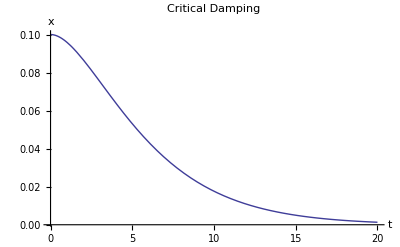

```mathematica
Plot[xCritical[t]/.CriticalDampedConditions,{t,0,20},PlotLabel->"Critical Damping",AxesLabel->{"t","x"},PlotRange->All]
```

The velocity of the critically damped oscillator  starts at v_0 and then slowly dies off.

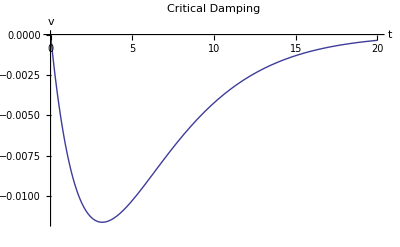

```mathematica
Plot[vCritical[t]/.CriticalDampedConditions,{t,0,20},PlotLabel->"Critical Damping",AxesLabel->{"t","v"},PlotRange->All]
```

The phase space plot shows the particle losing energy. The particle will end up at x=0 with zero velocity.

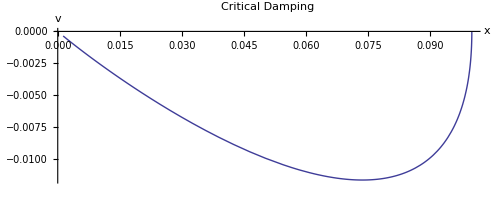

```mathematica
ParametricPlot[{First[xCritical[t]]/.CriticalDampedConditions,First[vCritical[t]]/.CriticalDampedConditions},{t,0,20},AxesLabel->{"x","v"},PlotLabel->"Critical Damping",PlotRange->All]
```

#### OverDamping

If γ>2ω the oscillator is overdamped. The conditions given below are for a slightly overdamped oscillator.

```mathematica
OverDampedConditions={x0->.1,m->.1,ω->√(k/m),v0->0,k->1,γ->2.1ω}
```

{x0→0.1,m→0.1,ω→√(k/m),v0→0,k→1,γ→2.1 ω}

Plotting the position and velocity of the object shows that the motion has the same basic features as in the critically damped cases but that the damping is much faster.  The function Chop has been used to eliminate small imaginary quantities that arise because machine arithmetic is done to only 16 places.

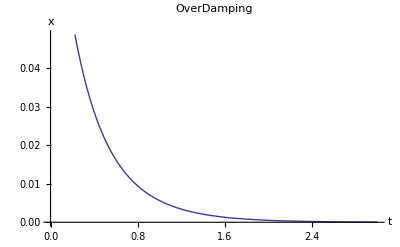

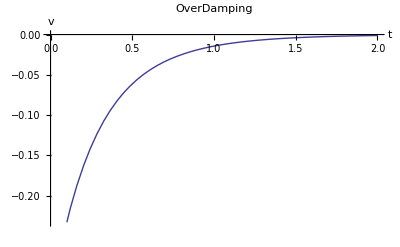

```mathematica
Plot[x[t]//.OverDampedConditions,{t,0,3},AxesLabel->{"t","x"},PlotLabel->"OverDamping"]
Plot[Simplify[Chop[v[t]//.OverDampedConditions]],{t,0,2},AxesLabel->{"t","v"},PlotLabel->"OverDamping"]
```

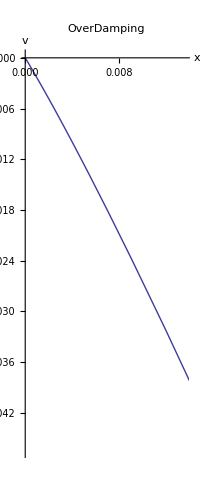

```mathematica
ParametricPlot[{x[t]//.OverDampedConditions,Chop[v[t]//.OverDampedConditions]},{t,0,5},AxesLabel->{"x","v"},PlotLabel->"OverDamping",AspectRatio->Full]
```

## Exercises

The assignment for Week 13 is to complete the following problems.  The submission should include your input code, the relevant outputs, and some sentences which explain the results.  The code should be self-contained and should run “in order”; that is, I should be able to simply run your notebook from beginning to end in order to reproduce your outputs.

### Problem One

From the following "data", find the starting conditions (x0 and v0), the angular frequency (ω), and the period (T) of the oscillator. What is the phase angle (ϕ) of the oscillator? What is the amplitude (A)? Like all real data this data is not perfect but contains some "experimental" error; address the uncertainties of your calculations. You may use any method that you like to answers these questions.

#### Data Set One

```mathematica
dataSet1={{0,0.5007776925563694},{0.5,0.07742815827440693},{1.,-0.413584076045498},{1.5,-0.970880077628931},{2.,-1.427905897450215},{2.5,-1.614187578884817},{3.,-1.873309477976028},{3.5,-2.125613127508216},{4.,-2.077313469733259},{4.5,-2.225554012692775},{5.,-2.061611821977329},{5.5,-1.749505039520971},{6.,-1.247817516855952},{6.5,-0.985048477974823},{7.,-0.3159756622310341},{7.5,0.1643852283418942},{8.,0.624324772578878},{8.5,1.096653472449683},{9.,1.55835001695052},{9.5,2.012382217257147},{10.,2.233827000161716},{10.5,2.359710166791859},{11.,2.419682428405658},{11.5,2.304856409123272},{12.,2.25886573337408},{12.5,1.859750478068737},{13.,1.48342571348667},{13.5,1.06579772626519},{14.,0.7267722015857766},{14.5,0.1612622907381281},{15.,-0.3812241116005161},{15.5,-0.7732634623668103},{16.,-1.17744653711769},{16.5,-1.6508772881197},{17.,-1.962422370149177},{17.5,-2.090302143351792},{18.,-2.267216994175503},{18.5,-2.158067825327134},{19.,-1.969035179061759},{19.5,-1.629114965868283},{20.,-1.336508990290723},{20.5,-0.835208360401679},{21.,-0.3514165153633562},{21.5,0.1452373685185685},{22.,0.6510632973657097},{22.5,1.013401529531922},{23.,1.464601152454333},{23.5,1.892557058408631},{24.,2.059083658448213},{24.5,2.252665499155034},{25.,2.358012070433671},{25.5,2.36307066555448},{26.,2.201601457443672},{26.5,2.012836180050034},{27.,1.729172138657275},{27.5,1.257514195492626},{28.,0.7374704040637625},{28.5,0.1533556902541086},{29.,-0.2627556743819337},{29.5,-0.853631191599124},{30.,-1.234658946971961},{30.5,-1.50473605361065},{31.,-1.984231016008978},{31.5,-2.105619747956838},{32.,-2.063942531348357},{32.5,-2.249722143635239},{33.,-2.048729763297899},{33.5,-1.719335929553208},{34.,-1.500065698979411},{34.5,-0.925258916057525},{35.,-0.4065005216048198},{35.5,0.1216557054449484},{36.,0.6276647313931692},{36.5,1.016133168453524},{37.,1.477957914315689},{37.5,1.83822731987168},{38.,2.139743723755296},{38.5,2.416103980648914},{39.,2.453236781637697},{39.5,2.454596086273386},{40.,2.36473183501149}};
```

### Problem Two

From the following "data" find the starting conditions (x0 and v0), the angular frequency (ω), and the period (T) of the oscillator. This data represents a damped oscillator. What is the phase angle (ϕ) of the oscillator? What is the amplitude (A)?  What is the damping parameter (γ)?  Like all real data this data is not perfect but contains some "experimental" error; address the uncertainties of your calculations. You may use any method that you like to answers these questions.

#### Data Set Two

```mathematica
dataSet2={{0,0.3193722795950542},{0.1,0.3550170947895908},{0.2,0.359319911305495},{0.3,0.3257610184406725},{0.4,0.2472255265198468},{0.5,0.1716209379381588},{0.6,0.06864677926733205},{0.7,-0.02861740736192995},{0.8,-0.1214332836364579},{0.9,-0.2125010299644887},{1.,-0.2666055454308553},{1.1,-0.2920439474515537},{1.2,-0.3042094508765891},{1.3,-0.2684347604534956},{1.4,-0.2028448636084926},{1.5,-0.1336555616840449},{1.6,-0.03641367813992585},{1.7,0.06066870100805117},{1.8,0.155640536898264},{1.900000000000001,0.2263182530489035},{2.,0.2753900119946367},{2.1,0.3073963958486089},{2.200000000000001,0.3045533742560063},{2.300000000000001,0.2785698195756387},{2.400000000000001,0.216576526178764},{2.500000000000001,0.1465178699416696},{2.600000000000001,0.05729247134027969},{2.700000000000001,-0.04955890944874731},{2.800000000000001,-0.1208789872280683},{2.900000000000001,-0.1930059509388532},{3.000000000000001,-0.2392471120378638},{3.100000000000001,-0.260499747126543},{3.200000000000001,-0.2490832090930726},{3.300000000000002,-0.2130392278057528},{3.400000000000002,-0.1629783669149952},{3.500000000000002,-0.0960278654438621},{3.600000000000002,-0.02059796126475917},{3.700000000000002,0.06282856280795223},{3.800000000000002,0.1284870816258542},{3.900000000000002,0.1975042417853844},{4.000000000000002,0.2551508112561441},{4.100000000000002,0.2740458531010875},{4.200000000000001,0.2524979789824213},{4.300000000000001,0.2334220716040493},{4.400000000000001,0.1764898117704854},{4.5,0.1041105570268226},{4.6,0.03848996565505525},{4.7,-0.03189902904900295},{4.799999999999999,-0.1018271691448462},{4.899999999999999,-0.1694826890669834},{4.999999999999999,-0.1952714085061705},{5.099999999999998,-0.2126367167465257},{5.199999999999998,-0.2169753344139136},{5.299999999999998,-0.1949171236102164},{5.399999999999997,-0.1356387967891012},{5.499999999999997,-0.07582428358441352},{5.599999999999996,0.0006895649657628067},{5.699999999999996,0.05852451279631652},{5.799999999999996,0.1369773763701157},{5.899999999999995,0.1897151584489439},{5.999999999999995,0.2105572844421678},{6.099999999999995,0.2354278229762269},{6.199999999999994,0.2271692765833738},{6.299999999999994,0.1932538066724886},{6.399999999999994,0.1442873122054465},{6.499999999999993,0.0975233399219265},{6.599999999999993,0.02291881129180233},{6.699999999999993,-0.03362721276600639},{6.799999999999992,-0.089557876366281},{6.899999999999992,-0.1437815405703866},{6.999999999999992,-0.1682840271932921},{7.099999999999991,-0.1768641959918271},{7.199999999999991,-0.190256758937183},{7.29999999999999,-0.1592448465664785},{7.39999999999999,-0.0974361710199097},{7.49999999999999,-0.06394978199565939},{7.599999999999989,0.01077317120905434},{7.699999999999989,0.05665892786622928},{7.799999999999989,0.1181335805450456},{7.899999999999988,0.1670046399006054},{7.999999999999988,0.2018569312069027},{8.09999999999999,0.2095899862778532},{8.19999999999999,0.1936482854944579},{8.29999999999999,0.1723479125514689},{8.39999999999999,0.1274452355013285},{8.49999999999999,0.0634990806764053},{8.59999999999999,0.02591076815416984},{8.69999999999999,-0.04395095830128753},{8.79999999999999,-0.0942399345852132},{8.89999999999998,-0.132347480240578},{8.99999999999998,-0.1534342598879324},{9.09999999999998,-0.1589631836216739},{9.19999999999998,-0.1531872244958797},{9.29999999999998,-0.1198608278083601},{9.39999999999998,-0.0841070619288202},{9.49999999999998,-0.03699821549112412},{9.59999999999998,0.00843640692236941},{9.69999999999998,0.06407207967884739},{9.79999999999998,0.1131144789284449},{9.89999999999998,0.1437273161559993},{9.99999999999998,0.1693100456127073},{10.09999999999998,0.1690519457129477},{10.19999999999998,0.1554784689823294},{10.29999999999998,0.145298338313565},{10.39999999999998,0.1052267393895641},{10.49999999999998,0.05579189231397569},{10.59999999999998,0.01031247961751554},{10.69999999999998,-0.02801390412396369},{10.79999999999998,-0.06933763485107383},{10.89999999999998,-0.1181953384967297},{10.99999999999998,-0.1280089301531122},{11.09999999999998,-0.1344700114316373},{11.19999999999998,-0.1235032245982427},{11.29999999999998,-0.0926741771159828},{11.39999999999997,-0.07709303346283342},{11.49999999999997,-0.03906275536648412},{11.59999999999997,0.01076620322412379},{11.69999999999997,0.05410447664896485},{11.79999999999997,0.1014355687027829},{11.89999999999997,0.1273947978391758},{11.99999999999997,0.1560234191440921}};
```